# VSINI

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\ELXMA\Desktop\UV\REMONTADA\cure\Nueva carpeta\20.11

```mathematica
vsini=Import["vsini.csv"]//Flatten;
```

```mathematica
Length@vsini
```

11818

```mathematica
Select[vsini,!NumberQ]
```

{}

```mathematica
Min@vsini
Max@vsini
Count[vsini,0]
```

0

29

133

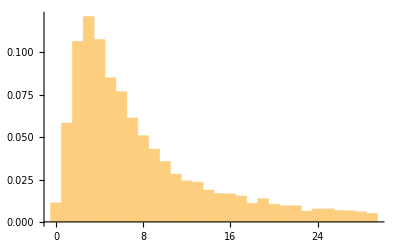

```mathematica
hi=Histogram[vsini,Automatic,"PDF"]
```

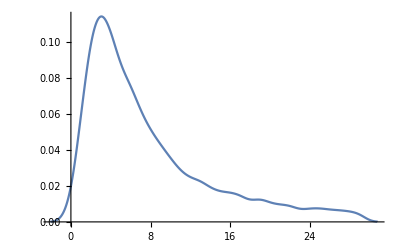

```mathematica
hsm=SmoothHistogram@vsini
```

```mathematica
dist0=SmoothKernelDistribution[vsini]
```

DataDistribution[…]

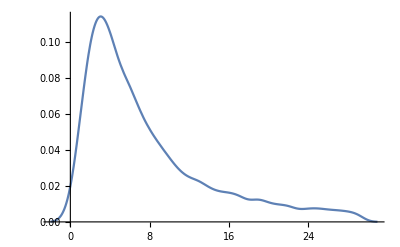

```mathematica
grd0=Plot[PDF[dist0,x],{x,-2,31}]
```

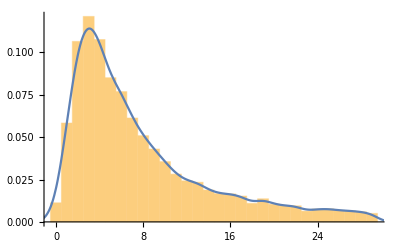

```mathematica
Show[hi,grd0]
```

Algunas formas de encontrar que la probabilidad de que la velocidad sea menor que 0

```mathematica
CDF[dist0,0]
```

0.0107542

```mathematica
NIntegrate[PDF[dist0,x],{x,-∞,0}]
```

0.0107542

```mathematica
Probability[x<0,x\[Distributed]dist0]
```

0.0107542

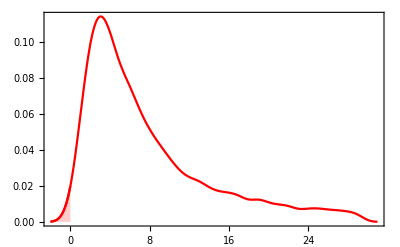

```mathematica
Show[Plot[PDF[dist0,x],{x,-2,31},PlotStyle->Red],Plot[PDF[dist0,x],{x,-2,0},Filling->Bottom,PlotStyle->Red],Frame->True]
```

Probabilidad de que sea mayor que o igual a 0

```mathematica
Probability[x>=0,x\[Distributed]dist0]
```

0.989246

```mathematica
NIntegrate[PDF[dist0,x],{x,0,∞}]
```

0.989246

```mathematica
dist1=SmoothKernelDistribution[vsini,Automatic,{"Bounded",{0,35},"Gaussian"}];
```

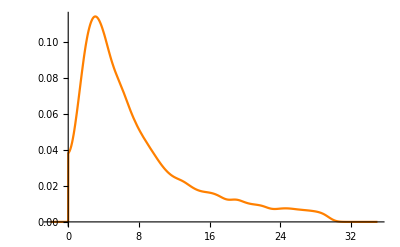

```mathematica
grd1=Plot[PDF[dist1,x],{x,-2,35},PlotStyle->Orange]
```

```mathematica
Probability[x<0,x\[Distributed]dist1]
```

0

```mathematica
Probability[x>0,x\[Distributed]dist1]
```

1.

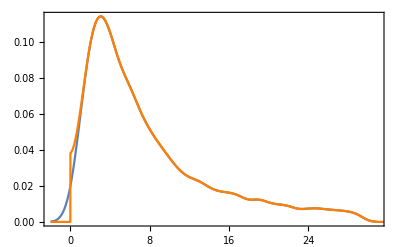

```mathematica
Show[grd0,grd1,Frame->True]
```

```mathematica
vsini2=-vsini;
```

```mathematica
dist2=SmoothKernelDistribution[vsini,Automatic,"Gaussian"];
```

```mathematica
dist3=SmoothKernelDistribution[vsini2,Automatic,"Gaussian"];
```

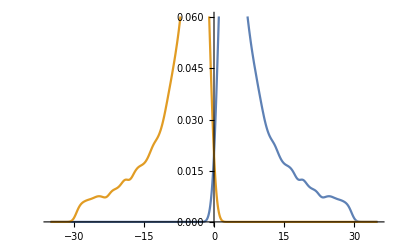

```mathematica
Plot[{PDF[dist2,x],PDF[dist3,x]},{x,-35,35}]
```

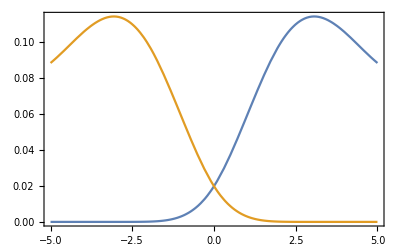

```mathematica
Plot[{PDF[dist2,x],PDF[dist3,x]},{x,-5,5},Frame->True]
```

```mathematica
dist4=ProbabilityDistribution[PDF[dist2,x]-PDF[dist3,x],{x,0,35}];
```

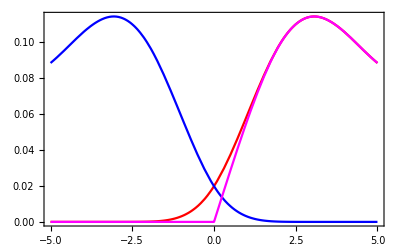

```mathematica
Plot[{PDF[dist2,x],PDF[dist3,x],PDF[dist4,x]},{x,-5,5},PlotStyle->{Red,Blue,Magenta},Frame->True]
```

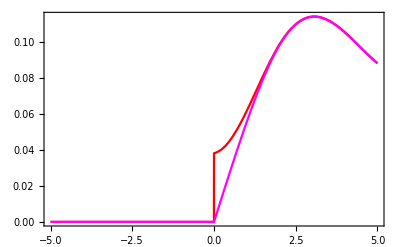

```mathematica
Plot[{PDF[dist1,x],PDF[dist4,x]},{x,-5,5},PlotStyle->{Red,Magenta},Frame->True]
```

```mathematica
cte=NIntegrate[PDF[dist4,x],{x,0,50}]
```

0.978492

```mathematica
dist5=ProbabilityDistribution[PDF[dist4,x]/cte,{x,0,35}];
```

```mathematica
NIntegrate[PDF[dist5,x],{x,0,50}]
```

1.

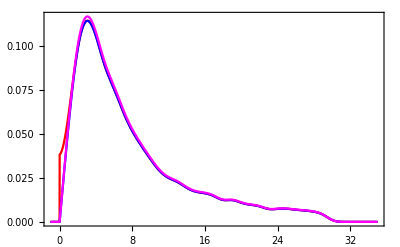

```mathematica
Plot[{PDF[dist1,x],PDF[dist4,x],PDF[dist5,x]},{x,-1,35},PlotStyle->{Red,Blue,Magenta},Frame->True]
```

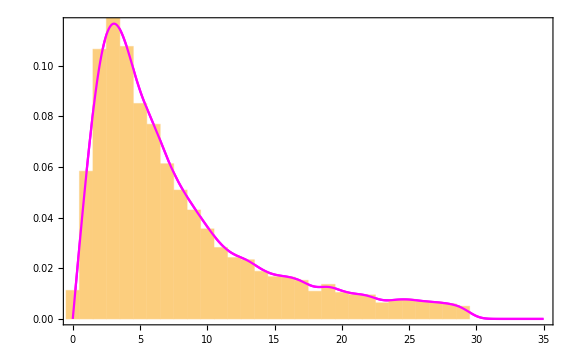

```mathematica
Show[Plot[PDF[dist5,x],{x,0,35},PlotStyle->Magenta],Histogram[vsini,Automatic,"PDF"],Plot[PDF[dist5,x],{x,0,35},PlotStyle->Magenta],Frame->True,ImageSize->Large]
```

## A partir de que distribución provienen los datos de VSINI

### Mínimos cuadrados

```mathematica
dist2N=FindDistribution[vsini,TargetFunctions->"Continuous"]
```

MixtureDistribution[{0.712421,0.287579},{NormalDistribution[4.45085,2.57368],NormalDistribution[14.5821,7.11049]}]

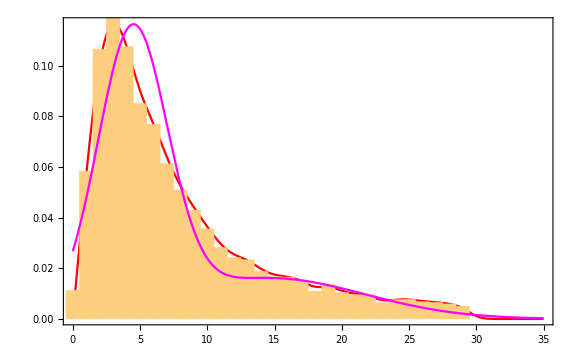

```mathematica
Show[Plot[PDF[dist5,x],{x,0,35},PlotStyle->Red],Histogram[vsini,Automatic,"PDF"],Plot[PDF[dist2N,x],{x,0,35},PlotStyle->Magenta],Frame->True,ImageSize->Large]
```

```mathematica
modelo=MixtureDistribution[{a1,a2},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2]}]
```

MixtureDistribution[{a1,a2},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2]}]

```mathematica
mincuad=ParallelSum[(PDF[dist5,vsini[[k]]]-PDF[modelo,vsini[[k]]])^2,{k,1,Length@vsini}];
```

```mathematica
solMC=NMinimize[mincuad,{{a1,0.1,.9},{a2,0.1,.9},{μ1,4.,5.},{σ1,2.,3.},{μ2,12.,17.},{σ2,5.,9.}},Method->"SimulatedAnnealing"]
```

{0.470675,{a1→0.507908,a2→1.061,μ1→3.11463,σ1→1.70988,μ2→6.75482,σ2→5.03249}}

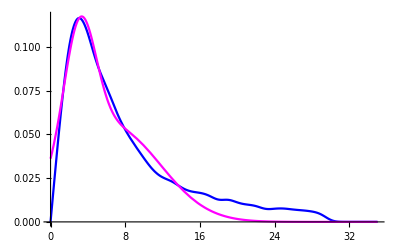

```mathematica
Plot[{PDF[dist5,x],PDF[modelo,x]/.solMC[[2]]},{x,0,35},PlotStyle->{Blue,Magenta}]
```

### Máxima verosimilitud

```mathematica
modelo=MixtureDistribution[{a1,a2},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2]}]
```

MixtureDistribution[{a1,a2},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2]}]

```mathematica
loglik=LogLikelihood[modelo,vsini];
```

```mathematica
solML=NMaximize[{Re@loglik,a1>0,a2>0},{{a1,0.1,.9},{a2,0.1,.9},{μ1,4.,5.},{σ1,2.,3.},{μ2,12.,17.},{σ2,5.,9.}},Method->"SimulatedAnnealing"]
```

{-35690.2,{a1→2.26384,a2→1.34726,μ1→4.1516,σ1→2.23115,μ2→13.7308,σ2→6.60134}}

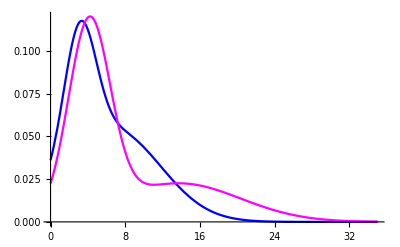

```mathematica
Plot[{PDF[modelo,x]/.solMC[[2]],PDF[modelo,x]/.solML[[2]]},{x,0,35},PlotStyle->{Blue,Magenta}]
```

```mathematica
solML=NMaximize[{Re@loglik,a1>0,a2>0},{{a1,0.1,.9},{a2,0.1,.9},{μ1,4.,5.},{σ1,2.,3.},{μ2,12.,17.},{σ2,5.,9.}},Method->"NelderMead"]
```

{-35690.2,{a1→0.304248,a2→0.181065,μ1→4.1516,σ1→2.23115,μ2→13.7308,σ2→6.60134}}

```mathematica
solML=NMaximize[{Re@loglik,a1>0,a2>0},{{a1,0.1,.9},{a2,0.1,.9},{μ1,4.,5.},{σ1,2.,3.},{μ2,12.,17.},{σ2,5.,9.}},Method->"DifferentialEvolution"]
```

NMaximize::nnum: The function value Indeterminate is not a number at {a1,a2,μ1,μ2,σ1,σ2} = {0.,0.,4.2913,13.8269,2.24668,6.53956}.

{-35691.,{a1→1.01073,a2→0.585392,μ1→4.13945,σ1→2.22881,μ2→13.8353,σ2→6.57494}}

```mathematica
solML=NMaximize[{Re@loglik,a1>0,a2>0,σ1>0,σ2>0},{{a1,0.1,.9},{a2,0.1,.9},{μ1,4.,5.},{σ1,2.,3.},{μ2,12.,17.},{σ2,5.,9.}},Method->"RandomSearch"]
```

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {a1,a2,μ1,μ2,σ1,σ2} = {16.0586,0.,8.10778,12.5973,0.,5.9538}.

Power::infy: Infinite expression 1/0.^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {a1,a2,μ1,μ2,σ1,σ2} = {16.0586,0.,8.10778,12.5973,0.,5.9538}.

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {a1,a2,μ1,μ2,σ1,σ2} = {26.4143,0.,7.67964,10.3068,0.,4.93001}.

General::stop: Further output of Experimental`NumericalFunction::nnum will be suppressed during this calculation.

{-35690.2,{a1→0.544183,a2→0.323856,μ1→4.1516,σ1→2.23115,μ2→13.7308,σ2→6.60134}}